## Anderson Neutrino Mass Model for Three Neutrinos.

```mathematica
(e^1)[t_,W_]:=RandomReal[{2t,2t+W},{o,o,K,K}] ;K=15;o=3;
(* K is the number of left and right fermion in a single generation and o is the number of generations of clockwork fermion. *)
```

```mathematica
t=1;W=5;
```

```mathematica
fg = (e^1)[t,W];
(* Randomly generating the values of e^ab for different generations and clockwork fermion. *)
```

```mathematica
hk = Table[0,{i,1,o},{j,1,o},{k,1,K},{h,1,K}];
(* Dummy tensor to store the values of e^ab and t^ab *)
```

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++,For[k=1,k<K+1,k++,hk[[i,j,k,k]] = fg[[i,j,k,k]]]];i++]
(* Assigning values e^ab to the elements of dummy tensor hk *)
```

```mathematica
a= Table[Subscript[p, i ,j],{i,1,o},{j,1,o}];
(* Dummy variables to store the values of t^ab , here a and b refers to generation of fermion. *)
```

```mathematica
i=1;While[i<o+1,{j=1;While[j<o+1,Subscript[p, i,j] = t;j++]};i++]
(* Assigning values to these t^ab *)
```

```mathematica
a;
(* Values of t^ab are stored as Subscript[p, a,b] *)
```

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++, For[k=1,k<K,k++,{hk[[i,j,k+1,k]] = a[[i,j]],hk[[i,j,k,k+1]] = a[[i,j]]}]];i++] 
(* Creating the tensor containing e^ab and t^ab as its components, in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

```mathematica
hk;
(* Tensor in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

### Converting rank 4 tensor hk to rank 2 matrix “mass mat” .

```mathematica
b = Table[Subscript[f, i,j] ,{i,1,o},{j,1,o}]
(* Creating the matrix that will store the elements of tensor hk as its elements *)
```

{{f_(1,1),f_(1,2),f_(1,3)},{f_(2,1),f_(2,2),f_(2,3)},{f_(3,1),f_(3,2),f_(3,3)}}

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++, b[[i,j]] = Table[0,{h,1,K},{l,1,K}]];i++]
(* Assigning dummy values 0 to these created matrix Subscript[b, i,j] *)
```

```mathematica
i=1; While[i<o+1,{j=1; While[j<o+1,For[q=1,q<K+1,q++,For[s=1,s<K+1,s++,b[[i,j]][[q,s]] = hk[[i,j,q,s]] ]];j++]};i++]
(* Assigning elements of hk as values to elements of matrix Subscript[b, i,j] *)
```

```mathematica
j=1;While[j<o+1,{i=2;While[i<o+1,b[[j,i]] = Join[b[[j,i-1]],b[[j,i]],2];i++]};j++]
```

```mathematica
(* Joining these matrix to form a bigger matrix. *)
```

```mathematica
i=2;While[i<o+1,b[[i,o]] = Join[b[[i-1,o]],b[[i,o]]];i++] 
(* Joining these matrix to form the final matrix that is consistent with tensor hk. *)
```

```mathematica
massmat = b[[o,o]]
(* This is the matrix Subscript[H, i,j]^(a,b) in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

{{4.54476,1,0,0,0,0,0,0,0,0,0,0,0,0,0,5.25862,1,0,0,0,0,0,0,0,0,0,0,0,0,0,4.22928,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,5.41496,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.93931,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.63046,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,3.25186,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.65203,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.55422,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,3.77828,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.88921,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.30206,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,2.62673,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.42164,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.38443,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,6.32735,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.17384,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.08925,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,6.41712,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.30949,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.48975,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,6.82877,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.40618,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.72512,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,6.00044,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.20041,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.30278,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,3.0141,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.07956,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.6642,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,3.2455,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.61914,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.47803,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,2.87277,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.32299,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.27915,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,2.24743,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.9562,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.23724,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,3.97603,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.1047,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.58583,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,6.8247,0,0,0,0,0,0,0,0,0,0,0,0,0,1,6.34149,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3.78734},{2.93218,1,0,0,0,0,0,0,0,0,0,0,0,0,0,6.5456,1,0,0,0,0,0,0,0,0,0,0,0,0,0,4.94307,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,6.97521,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.77918,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.05045,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,6.49672,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.91778,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.39853,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,3.4513,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.83177,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.77694,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,3.27399,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.01698,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.25544,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,5.84493,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.15669,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.6571,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,3.05978,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.6349,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.87391,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,6.52211,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.22875,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.14261,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,4.99041,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.5705,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.90496,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,6.7872,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.04944,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.30342,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,6.94191,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.22305,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.96851,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,5.43605,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.45082,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.60435,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,2.63526,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.12688,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.09017,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,2.05748,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.68866,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.89429,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,4.91399,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4.65772,0,0,0,0,0,0,0,0,0,0,0,0,0,1,5.99189},{2.4534,1,0,0,0,0,0,0,0,0,0,0,0,0,0,3.49161,1,0,0,0,0,0,0,0,0,0,0,0,0,0,6.23027,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,6.85501,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.99504,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.26361,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,5.49751,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.03611,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.55623,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,6.45849,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.02927,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.58682,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,4.65193,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.07095,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.31415,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,3.86856,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.54914,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.91242,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,6.59241,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.96097,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.14573,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,2.48402,1,0,0,0,0,0,0,0,0,0,0,0,0,1,2.27357,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.66965,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,6.55532,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.50285,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.07904,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,5.81341,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.44788,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.96344,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,2.83692,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.28749,1,0,0,0,0,0,0,0,0,0,0,0,0,1,4.04008,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,6.88314,1,0,0,0,0,0,0,0,0,0,0,0,0,1,3.32725,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.90443,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,3.77337,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.05416,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.1355,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,6.13852,1,0,0,0,0,0,0,0,0,0,0,0,0,1,5.74643,1,0,0,0,0,0,0,0,0,0,0,0,0,1,6.59408,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,2.84954,0,0,0,0,0,0,0,0,0,0,0,0,0,1,5.26738,0,0,0,0,0,0,0,0,0,0,0,0,0,1,5.02657}}

### Changing basis from L_i^a and R_j^b to (ψ_(L,k))^c and (ψ_(R,l))^d .

```mathematica
{u,w,v} = SingularValueDecomposition[massmat]; 
(* We are taking the SVD decomposition for above defined mass matrix to convert it to a basis where Subscript[L, i]^a basis can be converted to Subscript[(Subscript[ψ, L]^b), i] basis and Subscript[R, j]^b basis to Subscript[(Subscript[ψ, R]^c), j] basis. *)
```

```mathematica
New = Transpose[u].Table[Subscript[lo, n],{n,1,K*o}];  
(* This is the conversion of Subscript[L, i]^a basis to Subscript[(Subscript[ψ, L]^b), i] basis. *)
```

```mathematica
News = ConjugateTranspose[v].Table[Subscript[co, n],{n,1,K*o}];
(* This is the conversion of Subscript[R, j]^a basis to Subscript[(Subscript[ψ, R]^b), j] basis. *)
```

```mathematica
FullSimplify[Sum[w[[i,i]]*New[[i]]*News[[i]],{i,1,K*o}] ];
(* This is checking condition just to test change in basis under SVD took place properly. *)
```

```mathematica
loke= Simplify[Inverse[Transpose[u]]];
(*This gives the conversion of Subscript[(Subscript[ψ, L]^a), i] basis to Subscript[L, i]^b basis. Hence the components Subscript[v, 1,n] can be extracted from this matrix. *)
```

```mathematica
Roke = Simplify[Inverse[ConjugateTranspose[v]]];
(*This gives the conversion of Subscript[(Subscript[ψ, R]^a), i] basis to Subscript[R, i]^b basis. Hence the components Subscript[v, N,n] can be extracted from this matrix. *)
```

```mathematica
v1 = Table[i,{i,1,o}];
vN = Table[i,{i,1,o}];
mN = Table[i,{i,1,o}];
(* Defining two dummy list to store the values of components Subscript[v, 1,n] and Subscript[v, N,n] .  *)
```

```mathematica
i=1;While[i<o+1,v1[[i]]= Table[n,{n,1,K*o}];i++]
i=1;While[i<o+1,vN[[i]]= Table[n,{n,1,K*o}];i++]
(* For different o each element of v1 and vN have K*o values. *)
i=1;While[i<o+1,mN[[i]]= Table[n,{n,1,K}];i++]
```

```mathematica
j=1;While[j<o+1,{i=1;While[i<K*o+1,v1[[j]][[i]] = loke[[(j-1)*K+1,i]];i++]};j++]
j=1;While[j<o+1,{i=1;While[i<K*o+1,vN[[j]][[i]] = Roke[[(j-1)*K+K,i]];i++]};j++]
(*Assigning values to v1 and vN from the loke and roke matrix respectively. *)
j=1;While[j<o+1,{i=1;While[i<K+1,mN[[j]][[i]] = w[[(j-1)*K+i,(j-1)*K+i]];i++]};j++]
(* In mN , first term refers to different values of n for same value of o . *)
```

```mathematica
i=1;While[i<o+1,v1[[i]] = ArrayReshape[v1[[i]],{o,K}];i++]
i=1;While[i<o+1,vN[[i]] = ArrayReshape[vN[[i]],{o,K}];i++]
(* In v1 first component corresponds to first value of o for the output basis. In first component the first row corresponds to different n components in same input basis, Subscript[v, 1,n]^(o,o) and first column corresponds to different o for same component of n, Subscript[v, 1,1]^(o,o') . Same thing for vN i.e., in vN[[i]][[j,k]] i fixes α, j fixes β and k fixes n . alpha is in Subscript[R, N]^α and beta is in Subscript[ψ, R,n]^β . *)
```

```mathematica
w;
(* w matrix has as its diagonal, the values of Subscript[m, N]^(a,b) *)
```

### Defining mass matrix of full Lagrangian in ν^α , (ψ_(L,k))^c , (ψ_(R,l))^d and Ψ basis.

```mathematica
M =  Table[0,{x,2*o*K+4},{y,2*o*K+4}] ;(* This is the dummy matrix to store the values of mass matrix for full lagrangian in basis Subscript[(Subscript[ψ, L]^b), i]  and Subscript[(Subscript[ψ, R]^c), j]. *)
```

```mathematica
tN = Table[t,{i,1,3},{j,1,o}]
(* For the coupling of RN and neutrino, t^(α,a) *)
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
tvN = Table[0,{i,1,3},{j,1,o},{k,1,K}];
(* Creating a dummy matrix to store the value of tN^(α,a)*Subscript[v, N,n]^(a,b).
Here a and b comes from conversion of Subscript[R, N]^a to Subscript[(Subscript[ψ, R]^b), n] *)
```

```mathematica
l=1;While[l<K+1,{k=1;While[k<o+1,{j=1;While[j<4,tvN[[j,k,l]] = Sum[tN[[j,i]]*vN[[i,k,l]],{i,1,o}];j++]};k++]};l++]
```

```mathematica
(*Computing these values for tvN and storing them as rank 3 tensor. *)
```

```mathematica
tvN ;
(* In tvN[[i]][[j,k]] i fixes α of neutrino flavour, j fixes b and k fixes n .  b and n are in Subscript[ψ, R,n]^b . *)
```

```mathematica
t1 = Table[t,{i,1,o}];
(* For coupling of Subscript[L, 1]^a and ψ *)
```

```mathematica
tv1 = Table[0,{i,1,o},{j,1,K}];
(* Creating dummy matrix to store the values of t1^a*Subscript[v, 1,n]^(a,b) , Here a comes from Subscript[L, 1]^a and b comes from its conversion to Subscript[ψ, L,n]^b. *)
```

```mathematica
l=1;While[l<K+1,{k=1;While[k<o+1,tv1[[k,l]] = Sum[t1[[i]]*v1[[i,k,l]],{i,1,o}];k++]};l++] 
(* Assigning values to tv1 *)
```

```mathematica
tv1; (* Here first coordinate refers to β in output and second refers to its component n *)
```

```mathematica
tv1F = Flatten[tv1];
(* Flattening the above computed matrix to rank 1. *)
```

```mathematica
tvNF= ArrayReshape[tvN,{3,K*o}];
(* Flattening the rank 3 tvN to rank 2 matrix. *)
```

```mathematica
tvNF;
```

```mathematica
j=1;While[j<4,{i=1;While[i<K*o+1,{M[[j,K*o+3+i]] = tvNF[[j,i]],M[[K*o+3+i,j]] = tvNF[[j,i]]};i++]};j++]
i=1;While[i<K*o+1,{M[[4+2*K*o,3+i]] = tv1F[[i]],M[[3+i,4+2*K*o]] = tv1F[[i]]};i++]
i=1;While[i<K*o+1,{M[[3+i,3+K*o+i]] = w[[i,i]],M[[3+K*o+i,3+i]] = w[[i,i]]};i++]
M[[2*K*o+4,2*o*K+4]] = W;
(* Assigning values to the mass matrix of lagrangian in Subscript[(Subscript[ψ, L]^b), i]  and Subscript[(Subscript[ψ, R]^c), j] basis. *)
```

```mathematica
M;
```

```mathematica
Ev = Eigenvalues[M]
```

{20.6922,-20.6922,20.1977,-20.1977,19.6271,-19.626,19.2283,-19.2271,18.1182,-18.1163,16.7441,-16.7313,15.6734,-15.6688,14.4255,-14.4205,13.4721,-13.4599,12.9511,-12.9342,11.3856,-11.3775,10.1402,-10.1077,9.73742,-9.73051,8.83889,-8.83882,8.27909,-8.27688,4.89923,-3.90303,3.90303,-3.2096,3.2096,-2.98502,2.98502,2.96335,-2.96335,-2.89501,2.89501,-2.8191,2.8191,-2.75101,2.75101,-2.65135,2.65135,-2.57098,2.57097,-2.48466,2.48155,-2.41246,2.41246,-2.38089,2.38089,-2.30845,2.30844,-2.21283,2.21283,-2.12118,2.12118,-1.96762,1.96762,1.5514,-1.5514,-1.51459,1.51459,-1.45982,1.45872,-1.42742,1.42742,-1.34206,1.34206,-1.23317,1.23317,1.16428,-1.16428,-0.532439,0.532439,0.398992,-0.398992,-0.129441,0.129441,-0.129065,0.128963,-0.120187,0.120187,-0.053245,0.053245,-0.0408835,0.0405234,3.23137×10^-17,-3.84243×10^-18,6.23092×10^-19}

```mathematica
Ev[[-1]] ;
Ev[[-2]];
Ev[[-3]];
m12 = (Ev[[-2]]^2 -Ev[[-1]]^2)*Power[10,30] (*Current Experimental limit Subscript[Δm, 12]^2=7.53*10^-5 eV^2*)
m32 = (Ev[[-2]]^2 - Ev[[-3]]^2)*Power[10,30] (*Current Experimental limit Subscript[Δm, 32]^2=-2.32*10^-3 eV^2*)
```

0.000014376

-0.00102941

```mathematica
Eve = Eigenvectors[M];
Ieve = Inverse[Eve];
```

```mathematica
PMNS = Table[0,{i,1,3},{j,1,3}];
PMNS2 = Table[0,{i,1,3},{j,1,3}];
PMNS3 = Table[0,{i,1,3},{j,1,3}];
```

```mathematica
i=1;
While[i<4,{j=1;
While[j<4,{PMNS[[j,-i]]=Ieve[[j,-4+i]]};j++]};
i++] (*Following Normal Ordering*)(*Subscript[m, 1]^2<Subscript[m, 2]^2<Subscript[m, 3]^2*)
```

```mathematica
PMNS
```

(0.210491 | 0.788898 | -0.556718
0.57796 | -0.57674 | -0.556718
-0.788451 | -0.212159 | -0.556718)

```mathematica
PMNS2[[All,{1,2,3}]] = PMNS[[All,{2,3,1}]] (*Following Inverse Ordering*)(*Subscript[m, 3]^2<Subscript[m, 1]^2<Subscript[m, 2]^2*)
```

(0.788898 | -0.556718 | 0.210491
-0.57674 | -0.556718 | 0.57796
-0.212159 | -0.556718 | -0.788451)

```mathematica
PMNS3[[{1,2,3},All]] =PMNS2[[{3,2,1},All]]  (*Subscript[m, 3]^2<Subscript[m, 1]^2<Subscript[m, 2]^2*)(*Also Inverse Ordering*)
```

(-0.212159 | -0.556718 | -0.788451
-0.57674 | -0.556718 | 0.57796
0.788898 | -0.556718 | 0.210491)

We can see from result for W = 10 Petavolt and t of the order of W , we get mass of three neutrinos as of the order of 0.1 eV , with 4 generations and 10 clockwork fermions of both left and right kind in each generation.

```mathematica
Ev1 = Sort[Abs[ Ev]];
```

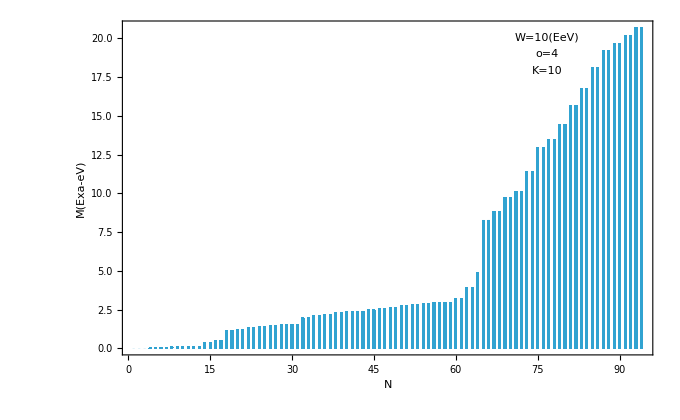

```mathematica
DiscretePlot[Ev1[[i]],{i,1,2*K*o+4},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","M(Exa-eV)"},LabelStyle->Directive[Bold, Medium],Epilog->{Text["o=4",Scaled[{0.8,0.90}]],Text["W=10(EeV)",Scaled[{0.8,0.95}]],{Text["K=10",Scaled[{.8,.85}]]}}]
```

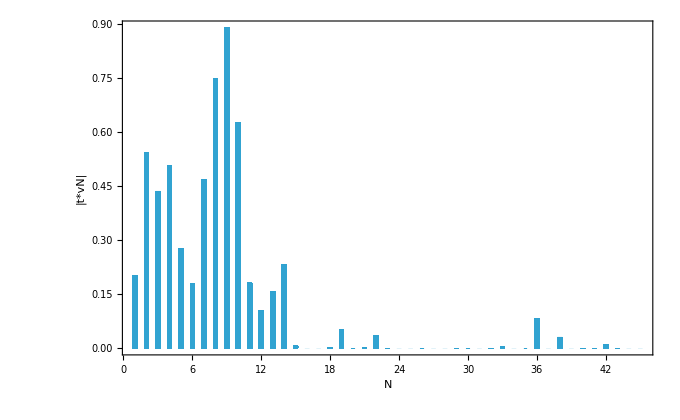

```mathematica
DiscretePlot[Abs[tvNF[[1,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}]
 (* Plot of interaction term t^1*Subscript[v, N,n]^α for neutrino 1. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

```mathematica
DiscretePlot[Abs[tvNF[[2,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}] (* Plot of interaction term t^2*Subscript[v, N,n]^α for neutrino 2. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

-Graphics-

```mathematica
DiscretePlot[Abs[tvNF[[3,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}] (* Plot of interaction term t^3*Subscript[v, N,n]^α for neutrino 3. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

-Graphics-